## grow-example.nb

Example Cellzilla2D notebook illustrating: 
	grow
	SimAnimate
	LineageAniamte
Portions of this notebook’s output have been suppressed (removed) to save space for internet display. All of the input cells included are sufficient to recover the output shown. 

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.92 (11-Nov-2012) loaded Wed 10 Apr 2013 08:42:26
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (3.0.18 (10-April-2013)) loaded Wed 10 Apr 2013 08:42:26
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

### Generate A Template of 8 cells

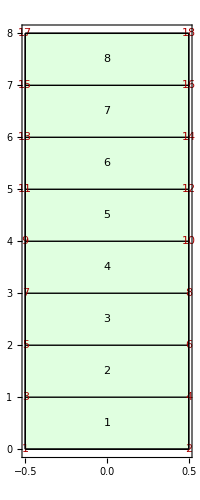

```mathematica
q=TemplateRectangular[{-1/2,1/2,1}, {0,8, 1}];
Q=Tissue2DTissue[q];
ShowTissue[Q,Frame-> True, "CellNumbers"-> True, "VertexNumbers"-> True]
```

### Define an internal pressure gradient in the template with the maximum in the second cell from the top and distributed via a bell curve

```mathematica
TC=Centroid[Q];
top=TissueVertices[Q][[18]];
f[i_]:=X[i]-> (BellCurve[1,top[[2]]-1.5,1.5][TC[[i,2]]]);
```

```mathematica
network={{∅->X,BellCurve[1, tip[2][t]-1.5,1.5][ycen[t]]}, {X-> ∅, 1}};
n=NTissueCells[Q];
centroids=Centroid[Q];
```

```mathematica
myic=f/@Range[n]
```

{X[1]→0.000335463,X[2]→0.00386592,X[3]→0.0285655,X[4]→0.135335,X[5]→0.411112,X[6]→0.800737,X[7]→1.,X[8]→0.800737}

### run the simulation for 100,000 time units

```mathematica
SIM=grow[Q,0,100000,
"center"-> cen,
"L1Anticlinal"-> False,
"Intercellular"-> {}, 
"IC"-> myic, 
"Walls"-> False, 
"mumax"-> 1, "mumin"-> 1,"muMaxDegrees"-> 90.0,
"IsotropicGrowth"-> False, 
"kmin"-> 1, "kmax"->1, "kMaxDegrees"-> 0, 
"IsotropicSprings"-> False, 
"TestCase"-> "Grow-Example", 
"IgnoreDivisionRadius"-> Infinity, 
"MaxRadius"-> Infinity, 
"Reactions"-> network, 
"Pumps"-> {},
"Diffusion"-> {}, 
"WallReactions"->{},
"BoundaryConditions"-> {X-> 0}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> {k, 1&}, 
"mu"-> {μ, .01(.1 + 10*(X[#1][t]+X[#2][t]))&},
"P"-> {P, .01*(.05+100*X[#][t])&}, 
"DivisionModel"-> "Errera",
"Parameters"-> {}, 
"DivisionThreshold"-> 1.1, 
"DivisionSigma"-> 0.10, 
"DivisionVariable"-> area, 
"MinAngleSpread"->135,
"Verbose"-> False, 
"Origin"-> {0, 0}, 
"ShowOptions"-> {Frame-> True,ImageSize-> 512, "CellNumbers"-> False, "EdgeNumbers"-> False, 
PlotRange-> {{-12.5,12.5}, {-5,25}}}
];
```

a lot of output is produced indicatiing several gigabytes of files that are written to disk. 

A new set of files is written for each cell division.

The simulation as shown consumes approximate 6 GB of disk space and generates 951 output files which are required to produce the subsequent movies for analysis. They consist of 	(1) Tissues after each cell division describing the cell geometry
	(2) Celerator reaction network for each tissue. 
	(3) Initial conditions for each tissue
	(4) Numerical solutions corresponding to (1) -> (3) until the next cell division is indicated. 
	(5) png snapshots at each cell division
	(6) Single notebooks consisting of lists of time spans; lists of run parameters; and cell lineages.

```mathematica
d="/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845";
```

```mathematica
SimAnimate[d,X,"Frames"-> 100, "Values"-> {0, 1.25}, "Colors"-> {White, Blue}, "ShowTime"-> False, BaseStyle-> {FontSize-> 22}, "ImageSize"-> 512, "ImageType"-> "jpg"]
```

Saving files to /home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-X-10Apr13-1504

ffmpeg -sameq -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

{/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-X-10Apr13-1504/Movie.mov}

```mathematica
LineageAnimate[d,"Frames"->100]
```

/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Lineage.nb

Saving files to /home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-Lineage-10Apr13-1517

ffmpeg -sameq -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

{/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-Lineage-10Apr13-1517/Movie.mov}